```mathematica
bigyellow = {297413941736400589979939780692294751544,4,1};
```

```mathematica
bigred = {201412842028162214137229450141139961424,4,1};
```

```mathematica
cands =DeleteDuplicates@ ;ru = cands[[13]]; ca = getca[cands[[13]], 200];
```

### Adaptive therapy

```mathematica
cps = getcancerperts[ru];
```

```mathematica
ip =cps[[2]];
ica = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, ip];
ilt = Replace[TestCALifeTime[ica], -Infinity:> 201];
iaps = Select[allperts[First[ica], ru[[2]]], Keys[#][[1, 1]]>= Keys[ip][[-1, 1]]&];
```

```mathematica
therapies = (*Table[*)
Module[{fitness =Infinity, ltgoal = TestLifetime[ru, 200], pca},
SeedRandom[333555];
NestList[
Function[{fitness, perts, aps},
pca = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, Join[perts, RandomChoice[aps]]];
plt = Replace[TestCALifeTime[First[pca]], -Infinity:> 201];
nf = Abs[plt - ltgoal];
If[nf < fitness, {nf, Join[perts, Last[pca]],Select[allperts[First[pca], ru[[2]]], Keys[#][[1, 1]]>= Keys[Last[pca]][[-1, 1]]&]}, {fitness, perts, aps}]
]@@#&, {Abs[ilt - ltgoal],ip, iaps},10][[All,2]]](*, {i, 2}]*);
```

```mathematica
GraphicsRow[PlotCA/@{ca, ica}]->GraphicsRow[PlotCA/@(PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, #[[1]]]&/@ Rest[Split[therapies]])]
```

-Graphics-→-Graphics-

#### On our blog pert

#### Trying moving n steps at a time

```mathematica
(*withinnsteps = 0<= Keys[Last[pca]][[-1, 1]] - Keys[#][[1, 1]]  <= nsteps&*)
```

```mathematica
nsteps = 20;
iaps = Select[allperts[First[ica], ru[[2]]], Keys[#][[1, 1]] - Keys[ip][[-1, 1]]  ==  nsteps&];
```

```mathematica
therapies = 
Table[
SeedRandom[333555 + i];
Module[{fitness =Infinity, ltgoal = TestLifetime[ru, 200], pca},
Nest[
Function[{fitness, perts, aps},
pca = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, Join[perts, RandomChoice[aps]]];
plt = Replace[TestCALifeTime[First[pca]], -Infinity:> 201];
nf = Abs[plt - ltgoal];
If[nf < fitness, {nf, Join[perts, Last[pca]],Select[allperts[First[pca], ru[[2]]],  Keys[#][[1, 1]]  - Keys[Last[pca]][[-1, 1]]==  Min[nsteps,plt -Keys[Last[pca]][[-1, 1]]]&]}, {fitness, perts, aps}]
]@@#&, {Abs[ilt - ltgoal],ip, iaps},10]][[2]], {i, 10}];
```

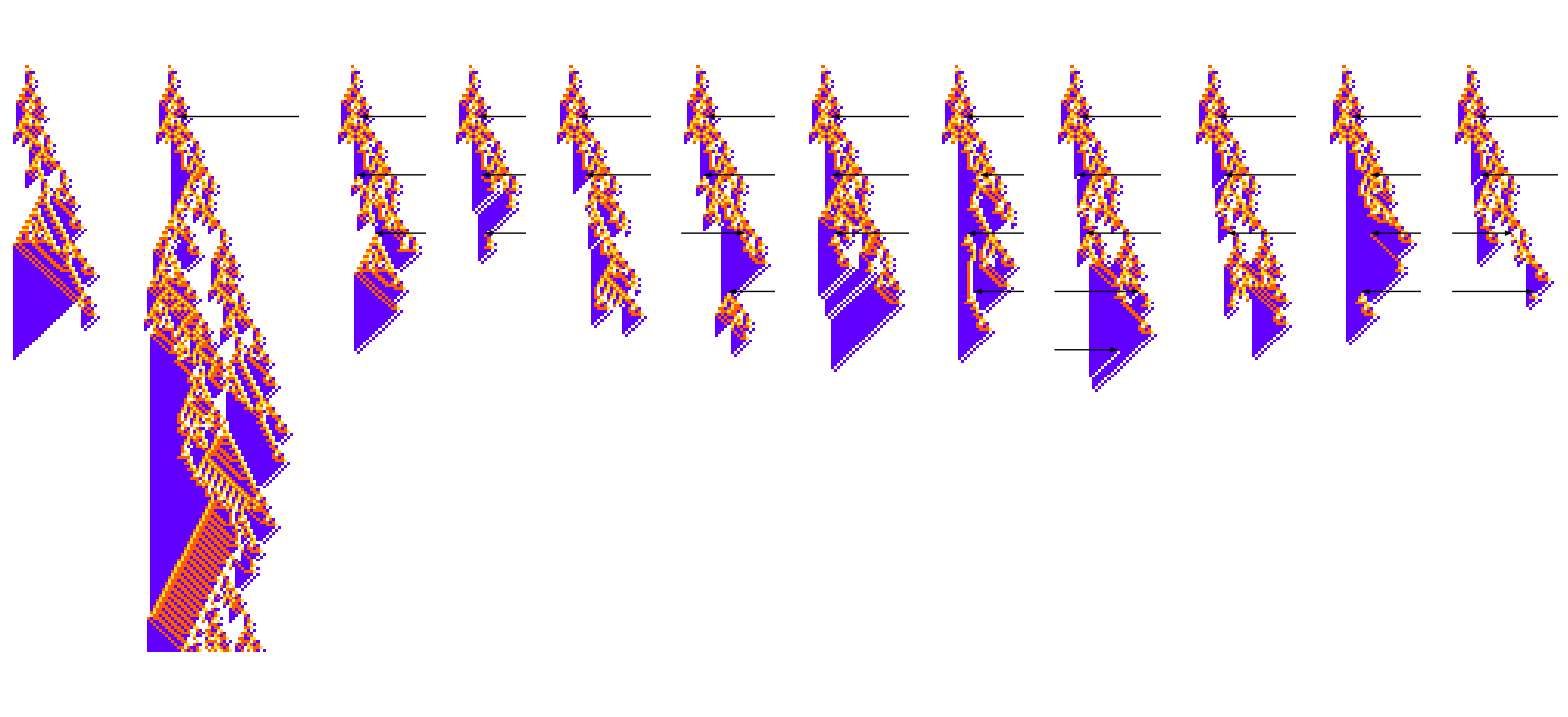

```mathematica
GraphicsRow[PlotCA/@Join[{ca, ica}, PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, #]&/@ therapies]]
```

### Multiple Perturbations

There’s way too many to do them all, better to just do random sample. We kind of already knew all this.

#### Disgusting

```mathematica
apsn = allpertnested[ru];
```

```mathematica
coms = Catenate[Table[{apsn[[i]], apsn[[j]]}, {i, 1, Length[apsn] - 1}, {j, i+1, Length[apsn]}]];
```

```mathematica
Nest[With[{c = RandomChoice[First[#]]}, {c, Delete[First[#], c]}]&,
```

```mathematica
Tuples/@RandomSample[coms, 1]
```

{{{<|{76,211}→0|>,<|{100,197}→0|>},{<|{76,211}→0|>,<|{100,197}→1|>},{<|{76,211}→0|>,<|{100,197}→3|>},{<|{76,211}→2|>,<|{100,197}→0|>},{<|{76,211}→2|>,<|{100,197}→1|>},{<|{76,211}→2|>,<|{100,197}→3|>},{<|{76,211}→3|>,<|{100,197}→0|>},{<|{76,211}→3|>,<|{100,197}→1|>},{<|{76,211}→3|>,<|{100,197}→3|>}}}

```mathematica
Tuples[{1, 2, 3}, 2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
coms[[1]]
```

{{<|{1,201}→0|>,<|{1,201}→2|>,<|{1,201}→3|>},{<|{2,202}→0|>,<|{2,202}→1|>,<|{2,202}→2|>}}

```mathematica
Tuples[apsn[[;;2]]]
```

{{<|{1,201}→0|>,<|{2,202}→0|>},{<|{1,201}→0|>,<|{2,202}→1|>},{<|{1,201}→0|>,<|{2,202}→2|>},{<|{1,201}→2|>,<|{2,202}→0|>},{<|{1,201}→2|>,<|{2,202}→1|>},{<|{1,201}→2|>,<|{2,202}→2|>},{<|{1,201}→3|>,<|{2,202}→0|>},{<|{1,201}→3|>,<|{2,202}→1|>},{<|{1,201}→3|>,<|{2,202}→2|>}}

```mathematica
aps = allperts[ru];
```

```mathematica
pairs = Table[{aps[[i]], aps[[j]]}, {i, 1, Length[aps[[;;3]]] - 1}, {j, i+1, Length[aps[[;;3]]]}];
```

```mathematica
allperts[ru]
```

#### Better

```mathematica
Join@@@Table[RandomSample[aps, 2], 10]
```

{<|{40,211}→3,{80,213}→3|>,<|{40,215}→1,{90,213}→2|>,<|{85,197}→0,{79,211}→3|>,<|{56,209}→3,{75,204}→3|>,<|{45,212}→1,{40,209}→2|>,<|{91,203}→1,{64,205}→2|>,<|{24,202}→3,{62,211}→1|>,<|{76,198}→0,{13,205}→3|>,<|{55,210}→1,{17,206}→2|>,<|{51,216}→1,{18,207}→2|>}

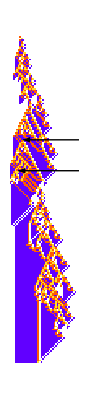
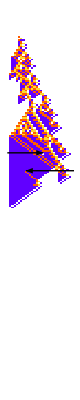
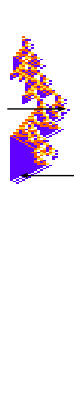
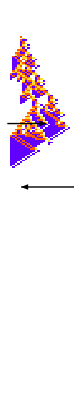
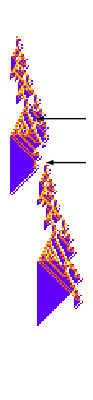
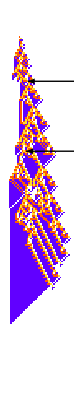
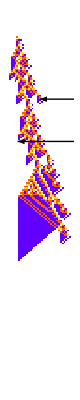
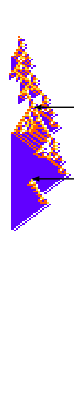

```mathematica
PlotCA[PerturbedCellularAutomaton[ru, {{1}, 0}, {200,{-200, 200}}, #]]&/@Join@@@Table[RandomSample[aps, 2], 10]
```

#### Even better

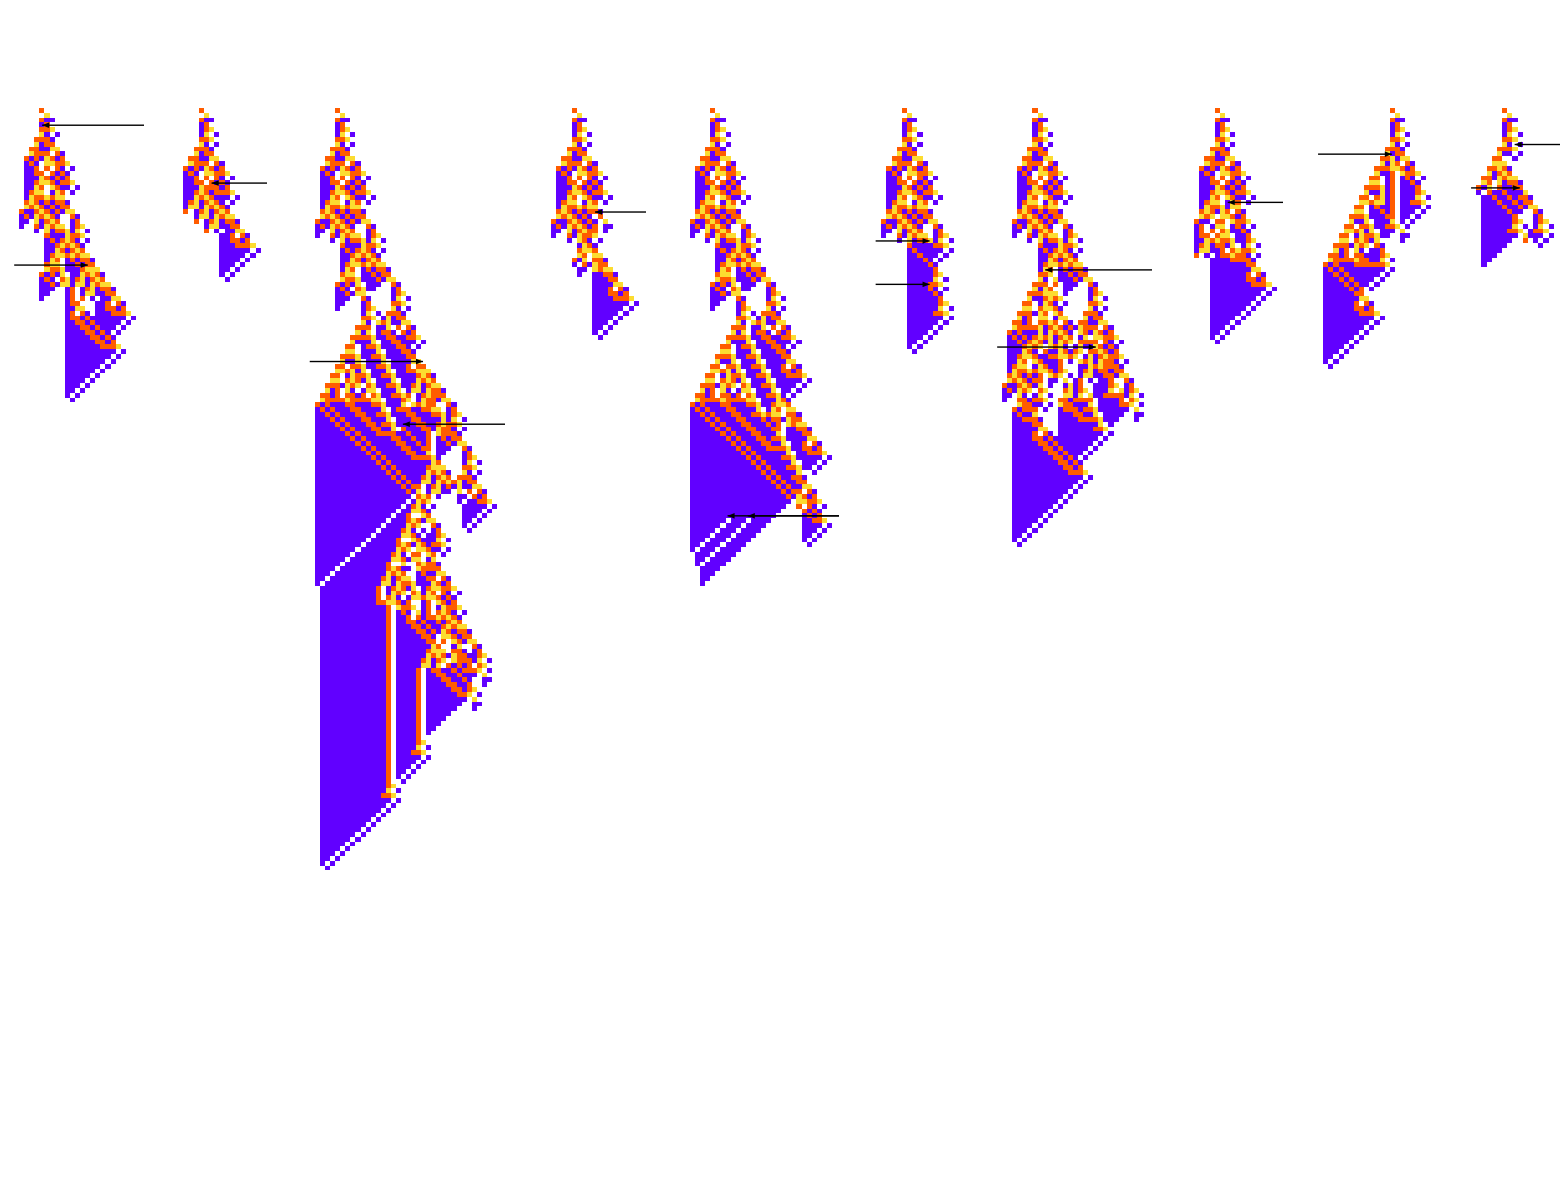

```mathematica
GraphicsRow[Table[PlotCA[PerturbedCellularAutomaton[ru, {{1}, 0}, {200,{-200, 200}}, 2]], 10]]
```

two perts

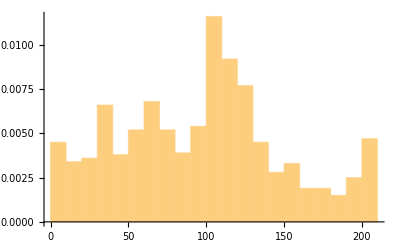

```mathematica
Histogram[Table[TestCALifeTime[PerturbedCellularAutomaton[ru, {{1}, 0}, {200,{-200, 200}}, 2, "ReturnPerturbations"->False]]/.-Infinity:> 202, 1000], {10}, "PDF"]
```

Survivial

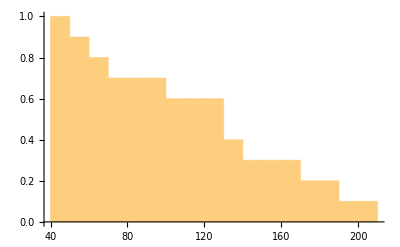

```mathematica
Histogram[Table[TestCALifeTime[PerturbedCellularAutomaton[ru, {{1}, 0}, {200,{-200, 200}}, 2, "ReturnPerturbations"->False]]/.-Infinity:> 202, 10], {10},"SF"]
```

Mortality

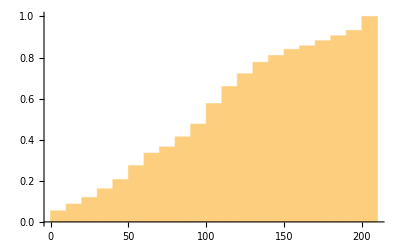

```mathematica
Histogram[Table[TestCALifeTime[PerturbedCellularAutomaton[ru, {{1}, 0}, {200,{-200, 200}}, 2, "ReturnPerturbations"->False]]/.-Infinity:> 202, 1000], {10}, "CDF"]
```

#### n perts

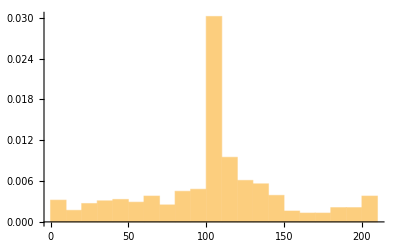
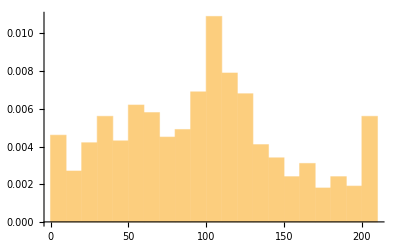
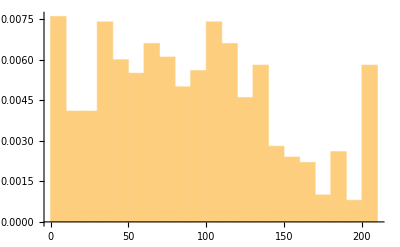
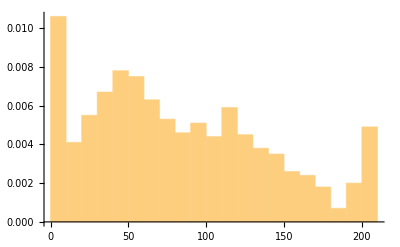
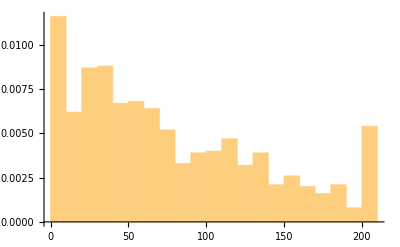
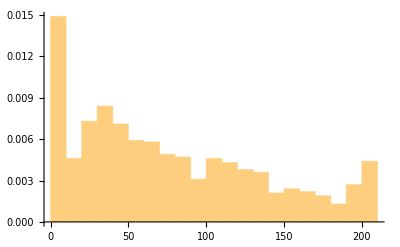
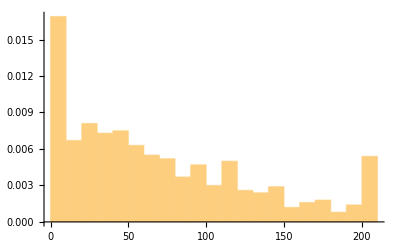
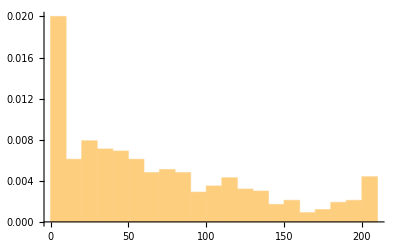

```mathematica
Table[Histogram[Table[TestCALifeTime[PerturbedCellularAutomaton[ru, {{1}, 0}, {200,{-200, 200}}, i, "ReturnPerturbations"->False]]/.-Infinity:> 202, 1000], {10}, "PDF"], {i, 10}]
```

### Scratchpad for puttiing new func in draft

```mathematica
pcas = PerturbedCellularAutomaton[ru, {{1}, 0}, {150, {-10, 50}}, #, "ReturnPerturbations"->False]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 50}}]];
```

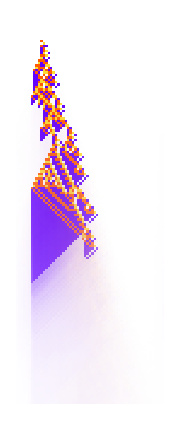

```mathematica
ArrayPlot[btpcas=Map[Blend[{GrayLevel[1],Hue[0.06, 1, 1],Hue[0.73, 1, 1],Hue[0.14, 0.81, 0.99]},BinCounts[#,{0,4,1}]]&,Transpose[pcas,{3,1,2}],{2}]]
```

```mathematica
lts =  Block[{ru = {299459058088077823758143088095350287424,4,1}, ca},
ca = CellularAutomaton[ru, {{1}, 0}, {200, {-200, 200}}];
TestCALifeTime/@(PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-200, 200}}, #, "ReturnPerturbations"->False]&/@ allperts[ca, 4])];
```

```mathematica
lts500 =  Block[{ru = {299459058088077823758143088095350287424,4,1}, ca},
ca = CellularAutomaton[ru, {{1}, 0}, {500, {-500, 500}}];
TestCALifeTime/@ParallelMap[PerturbedCellularAutomaton[ru, {{1}, 0}, {500, {-500, 500}}, #, "ReturnPerturbations"->False]&, allperts[ca, 4]]];
```

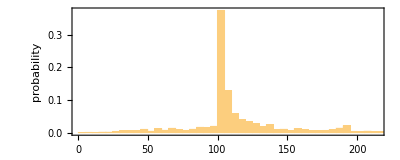

```mathematica
Histogram[lts500, 100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}, PlotRange->{{0, 215}, Automatic}]
```

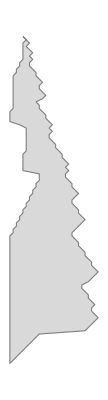

```mathematica
Graphics[{EdgeForm[Gray],LightGray,CAPolygon[CellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-10, 50}}]]}]
```

```mathematica
Show[]
```

```mathematica
With[{ru ={299459058088077823758143088095350287424,4,1}, init ={{1}, 0},  txspec =  {110, {-10, 50}}}, Show[PlotCA[PerturbedCellularAutomaton[ru, init, txspec]], Graphics[{EdgeForm[Gray],LightGray,CAPolygon[CellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-10, 50}}]]}]]]
```

-Graphics-

```mathematica
ByteCount[allperts[ru]]
```

1404360

```mathematica
TestCALifeTime/@(PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]&/@ allperts[ru,init,txspec])]
```

$Aborted

```mathematica
CountsBy[]
```

```mathematica
data=RandomInteger[{0,1},{20,20}];

(*Define the magnification region and magnified data*)
magnifiedRegion={{5,10},{5,10}}; (*Row and column bounds*)
magnifiedData=data[[Sequence@@magnifiedRegion]];

(*Main ArrayPlot*)
ArrayPlot[data,Frame->True,PlotRangePadding->None,ImageSize->400,Epilog->{(*Draw the rectangle around the magnified region*)Style[Rectangle[Reverse@magnifiedRegion[[1]]-{0.5,0.5},Reverse@magnifiedRegion[[2]]-{0.5,0.5}],Red,Thick],(*Add the magnified plot as an inset*)Inset[ArrayPlot[magnifiedData,ImageSize->Scaled[0.2],Frame->True],{15,15},(*Position of the inset in the main ArrayPlot*){Left,Bottom}]}]
```

-Graphics-

### 3D magnification

```mathematica
Graphics3D[{{Texture[Normal[PlotCA[{PerturbedCellularAutomaton[ru,{{1},0},{{8, 24},{-200,200}},{15,206}->0, "ReturnPerturbations"->False],<|{15 - 8 + 1, 206}->0|>},Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,150}, "MaxWidth"->{196, 210}, "Trim"->{None, None}, "ArrowSize"->Large, "ArrowDirection"->"Left"]]], Polygon[{{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}] }}]
```

-Graphics3D-

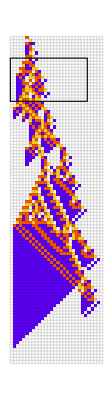
-Graphics-
-Graphics-

```mathematica
Column[{ImageTake[PlotCA[ru,"Steps"->105,ImageSize->{{1, 3000}, {1, 1500}},Mesh->All,MeshStyle->Opacity[.1]],  {100, 300}, {1, 260}], Show[PlotCA[ru,"Steps"->105,ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1]], Graphics[{EdgeForm@Black, FaceForm@None, Rectangle[{0, 85}, {25, 99}]}]]}]
```

### For blog

```mathematica
ip =cps[[2]];
ica = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, ip];
ilt = Replace[TestCALifeTime[ica], -Infinity:> 201];
iaps = Select[allperts[First[ica], ru[[2]]], Keys[#][[1, 1]]>= Keys[ip][[-1, 1]]&];
```

```mathematica
therapies = (*Table[*)
Module[{fitness =Infinity, ltgoal = TestLifetime[ru, 200], pca},
SeedRandom[333555];
NestList[
Function[{fitness, perts, aps},
pca = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, Join[perts, RandomChoice[aps]]];
plt = Replace[TestCALifeTime[First[pca]], -Infinity:> 201];
nf = Abs[plt - ltgoal];
If[nf < fitness, {nf, Join[perts, Last[pca]],Select[allperts[First[pca], ru[[2]]], Keys[#][[1, 1]]>= Keys[Last[pca]][[-1, 1]]&]}, {fitness, perts, aps}]
]@@#&, {Abs[ilt - ltgoal],ip, iaps},10][[All,2]]](*, {i, 2}]*);
```

```mathematica
GraphicsRow[PlotCA/@{ca, ica}]->GraphicsRow[PlotCA/@(PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, #[[1]]]&/@ Rest[Split[therapies]])]
```

-Graphics-→-Graphics-

#### Blog pert

```mathematica
ip =<|{23,111}->2|>
ica = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}, ip];
ilt = Replace[TestCALifeTime[ica], -Infinity:> 201];
iaps = Select[allperts[First[ica], ru[[2]]], Keys[#][[1, 1]]>= Keys[ip][[-1, 1]]&];
```

<|{23,111}→2|>

```mathematica
therapies = Table[
Module[{ru ={299459058088077823758143088095350287424,4,1}, fitness =Infinity, ltgoal = TestLifetime[ru, 200], pca},
SeedRandom[333557 + i];
NestList[
Function[{fitness, perts, aps},
pca = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}, Join[perts, RandomChoice[aps]]];
plt = Replace[TestCALifeTime[First[pca]], -Infinity:> 201];
nf = Abs[plt - ltgoal];
If[nf < fitness, {nf, Join[perts, Last[pca]],Select[allperts[First[pca], ru[[2]]], Keys[#][[1, 1]]>= Keys[Last[pca]][[-1, 1]]&]}, {fitness, perts, aps}]
]@@#&, {Abs[ilt - ltgoal],ip, iaps},10][[All,2]]], {i, 10}];
```

```mathematica
Grid[Partition[#, 2]&[(GraphicsRow[PlotCA/@{ca, ica}]->GraphicsRow[PlotCA/@(PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {200, {-110, 110}}, #[[1]]]&/@ Rest[Split[#]])]&)/@therapies]]
```

-Graphics-→-Graphics- | -Graphics-→-Graphics-
-Graphics-→-Graphics- | -Graphics-→-Graphics-
-Graphics-→-Graphics- | -Graphics-→-Graphics-
-Graphics-→-Graphics- | -Graphics-→-Graphics-
-Graphics-→-Graphics- | -Graphics-→-Graphics-

#### Plotting red dots

```mathematica
InitSearchX[ru_,iwid_,max_:200,steps_:1000]:=Reap[Last/@With[{fun=(Sow[If[#==0,-Infinity,max-#+1]]&[LengthWhile[Reverse[CellularAutomaton[ru,{#,0},max]],Total[#]==0&]]&)},NestList[With[{mm=MapAt[Mod[#+RandomInteger[{1,ru[[2]]-1}],ru[[2]]]&,#[[1]],RandomInteger[{1,iwid}]]},With[{life=fun[mm]},If[life>=#[[2]],{mm,life},#]]]&,{#,fun[#]}&@CenterArray[{1},iwid],steps]]]
```

```mathematica
Show[ListStepPlot[First[#],Frame->True,AspectRatio->.4],ListPlot[Last[#],PlotStyle->Red]]&[SeedRandom[1246491777835];InitSearchX[{1246491453600,3,1},10,200,100]]
```

#### Predicting based treatment based on width

#### Predicting from previous widths